## General

### Run This to browse

```mathematica
Manipulate[plotROC[funcname, xnoise, ynoise, nsamp, nbin],{funcname,Union[functionName/@rocFileNames]}, {xnoise,Union[xNoise/@rocFileNames]}, {ynoise,Union[yNoise/@rocFileNames]}, {nsamp,Union[nSamples/@rocFileNames]}, {nbin,Union[nBins/@rocFileNames]}]
```

### Code

```mathematica
rocFileNames=FileNames["*.roc.tsv",{"../rocs"}];
```

```mathematica
rocFileNames[[1]]
```

../rocs/00001_parabolic_x000_y000.s005.b001.roc.tsv

```mathematica
rocFileNames[[140]]
```

../rocs/00001_parabolic_x000_y010.s006.b001.roc.tsv

```mathematica
rocFileNames[[440]]
```

../rocs/00001_parabolic_x010_y000.s010.b010.roc.tsv

```mathematica
StringSplit[rocFileNames[[1]],"_"]
```

{../rocs/00001,parabolic,x000,y000.s005.b001.roc.tsv}

```mathematica
functionName[filename_String]:=StringSplit[filename,"_"][[2]]
```

```mathematica
xNoise[filename_String]:=ToExpression[StringDrop[StringSplit[filename,"_"][[3]],1]]/100
```

```mathematica
xNoise[rocFileNames[[1]]]
```

0

```mathematica
xNoise[rocFileNames[[440]]]
```

1/10

```mathematica
yNoise[filename_String]:=ToExpression[StringDrop[StringSplit[StringSplit[filename,"_"][[4]],"."][[1]],1]]/100
```

```mathematica
yNoise[rocFileNames[[440]]]
```

0

```mathematica
yNoise[rocFileNames[[140]]]
```

1/10

```mathematica
nSamples[filename_String]:=ToExpression[StringDrop[StringSplit[StringSplit[filename,"_"][[4]],"."][[2]],1]]
```

```mathematica
nSamples[rocFileNames[[440]]]
```

10

```mathematica
nSamples[rocFileNames[[140]]]
```

6

```mathematica
nBins[filename_String]:=ToExpression[StringDrop[StringSplit[StringSplit[filename,"_"][[4]],"."][[3]],1]]
```

```mathematica
nBins[rocFileNames[[440]]]
```

10

```mathematica
nBins[rocFileNames[[140]]]
```

1

```mathematica
plotROC[funcname_, xnoise_, ynoise_, nsamp_, nbin_]:=With[{filenames=Select[rocFileNames,functionName[#]==funcname&&xNoise[#]==xnoise&&yNoise[#]==ynoise&&nSamples[#]==nsamp&&nBins[#]==nbin&]},If[Length[filenames]==0,"The requested ROC curve has not been calculated",
With[{data=Import[filenames[[1]]]},ListLinePlot[data,PlotRange->All]
]]]
```

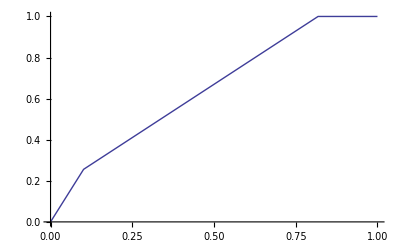

```mathematica
plotROC["parabolic",0,0,6,4]
```

## L-shaped

```mathematica
Needs["PlotLegends`"]
```

```mathematica
l10106020=Import["../rocs/00350_L_x010_y010.s060.b020.roc.tsv"];
```

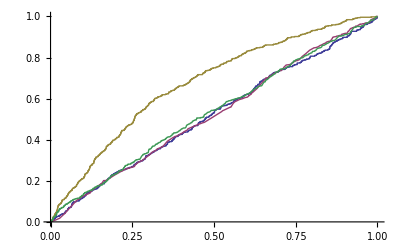

```mathematica
ListLinePlot[{l10106020,l10103018,l10103001,l10103002},PlotLegend->{20,18,"DCor","Spear"},LegendPosition->{0.5,-0.45}]
```

```mathematica
l10103018=Import["../rocs/00350_L_x010_y010.s030.b018.roc.tsv"];
```

```mathematica
l10103001=Import["../rocs/00350_L_x010_y010.s030.b001.roc.tsv"];
```

```mathematica
l10103002=Import["../rocs/00350_L_x010_y010.s030.b002.roc.tsv"];
```

## Parabola w 0.1 0.1 noise

```mathematica
p10106020=Import["../rocs/00001_parabolic_x010_y010.s060.b020.roc.tsv"];
```

```mathematica
p10103018=Import["../rocs/00001_parabolic_x010_y010.s030.b018.roc.tsv"];
```

```mathematica
p10103001=Import["../rocs/00001_parabolic_x010_y010.s030.b001.roc.tsv"];
```

```mathematica
p10103002=Import["../rocs/00001_parabolic_x010_y010.s030.b002.roc.tsv"];
```

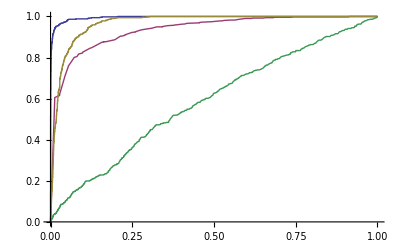

```mathematica
ListLinePlot[{p10106020,p10103018,p10103001,p10103002},PlotRange->All, PlotLegend->{20,18,"DCor","Spear"},LegendPosition->{0.5,-0.45}]
```